```mathematica
Clear["Global`*"]
```

```mathematica
u[0]=1;
n=100;δ=0.02/n;
```

```mathematica
V[r_]:=-1/r+Subscript[V, s][r]
Subscript[V, s][r_]:=1/r^3
```

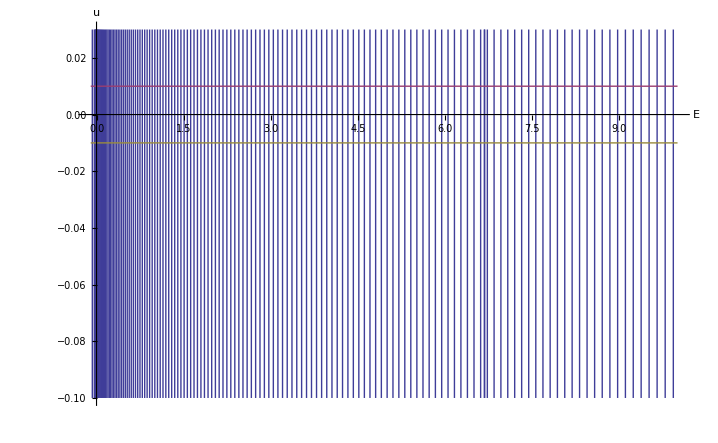

```mathematica
f[Ε_?NumberQ]:=Block[{u,r,r1=0.0001,r2=100},First[u[r2]/.NDSolve[{D[u[r], r,r]+(2(Ε-V[r])+1/r^2)u[r]==0,u[r1]==0.01,u'[r1]==√(2(V[r1]-Ε))*u[r1]},u,{r,r1,r2}]]]
Plot[{f[Ε],0.01,-0.01},{Ε,-0.1,10},PlotRange->{{-1,1},{3*0.01,-10*0.01}},AxesLabel->{"E","u"}]
```